```mathematica
(*Define some useful functions, kr as a function of the IR cut off Λ, and yukawa a function of the c's and Λ which returns the value of the fermion yukawa couplings*)
kr[Λ_]:= Log[(2435/1000*10^18)/Λ]/π;
yukawa[c_,Λ_]:=((.5 - c)Exp[(1 - 2c)π kr[Λ]])/(Exp[(1-2c)π kr[Λ]] - 1);
```

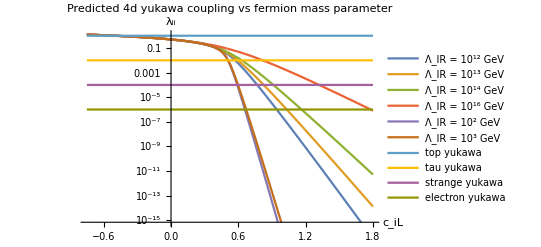

```mathematica
(*Let's look at fermion yukawa couplings vs 5d mass paremeter for different values of the IR cutoff. We see the start difference between having a TeV cutoff, and having a Seesaw cutoff. When we raise the IR cutoff, we can move the fermions further and further away, towards the planck brane. No matter what happens the top quark ALWAYS lives at c = -1/2*)

LogPlot[{yukawa[x,10^12], yukawa[x,10^13],yukawa[x,10^14],yukawa[x,10^16],yukawa[x,10^2], yukawa[x,10^3], top = 1, tau = 10^-2,strange = 10^-4, elec = 10^-6},{x,-.75,1.8}, PlotLegends->{"Λ_IR = 10^12 GeV","Λ_IR = 10^13 GeV","Λ_IR = 10^14 GeV", "Λ_IR = 10^16 GeV","Λ_IR = 10^2 GeV", "Λ_IR = 10^3 GeV","top yukawa","tau yukawa","strange yukawa","electron yukawa"}, AxesLabel->{Style["c_iL",16],Style["λ_ii",16]}, PlotLabel->Style["Predicted 4d yukawa coupling vs fermion mass parameter",18,Black]]
```

```mathematica
(*This function solves for the value of c which gives the yukawa coupling y, given that the IR scale is Λ*)
Csolve[Λ_, y_]:=c/.FindRoot[yukawa[c,Λ] == y,{c,0}];
```

```mathematica
(*Ok now let's look at Proton Decay. First define the normalization function for the fermions*)
```

```mathematica
Ninv[c_,Λ_]:= Sqrt[(1/2 - c)/(Exp[(1 - 2c)π kr[Λ]] - 1)];
```

```mathematica
(*Now calculate the suppression scale for the generic 4 fermion operator, abcd are the 5d mass parameters for each fermion*)
Suppression[a_,b_,c_,d_, Λ_]:= Sqrt[(2(1-Exp[-2π kr[Λ]]))/((2.435*10^18)^2) Ninv[a, Λ] Ninv[b, Λ] Ninv[c, Λ] Ninv[d, Λ] (Exp[(4 - a - b - c - d )π kr[Λ]] - 1)/(4 - a -b -c -d)];
```

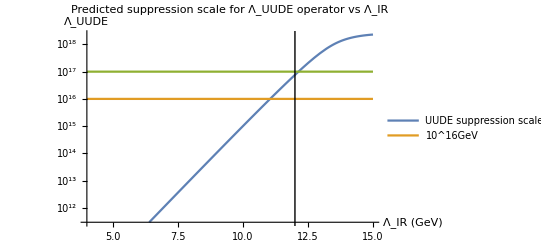

```mathematica
(*Let's plot this suppression scale for the UUDE four fermion operator vs Subscript[Λ, IR]*)
LogPlot[{y = 1/Suppression[Csolve[10^logΛ,10^-5], Csolve[10^logΛ,10^-5], Csolve[10^logΛ,2*10^-5], Csolve[10^logΛ,10^-6], 10^logΛ],y = 10^16,y=10^17}, {logΛ, 4,15},Epilog->{InfiniteLine[{12,0},{0,1}]},PlotLegends->{"UUDE suppression scale GeV","10^16GeV"}, PlotLabel->Style["Predicted suppression scale for Λ_UUDE operator vs Λ_IR",18,Black],AxesLabel->{Style["Λ_IR (GeV)",16, Black],Style["Λ_UUDE",16,Black]}]
```